```mathematica
dir=NotebookDirectory[];
a=SetDirectory[dir]
date = DateString[Riffle[{"Month","Day"},"_"]]
```

D:\Curve Elasticity\Simulation\2026\jan\results\helicoidC\st ver - Copy

09_22

```mathematica
gb=1
X[u_,v_]:={u Cos[v], u Sin[v],v};
uu=Import["uu_2_26_"<>date<>".txt","Table"];
vv=Import["vv_2_26_"<>date<>".txt","Table"];
uu=Flatten[uu];
vv=Flatten[vv];
points=MapThread[X,{uu,vv}];
V2k=Graphics3D[{Yellow,Thickness[0.01],Line[points]},Boxed->False];

V3=ParametricPlot3D[X[u,v],{u,-Pi,5},{v,-Pi,2Pi},PlotStyle->Directive[LightRed]];

Show[ V3,V2k,PlotRange->All]
```

1

-Graphics3D-

```mathematica
X[u_,v_]:={u Cos[v],u Sin[v],c v};
(*First derivatives*)
Xu=D[X[u,v],u]
Xv=D[X[u,v],v]

(*Second derivatives*)
Xuu=D[X[u,v],{u,2}];
Xuv=D[Xu,v];
Xvv=D[X[u,v],{v,2}];

(*Normal vector to surface*)
nVec=Cross[Xu,Xv]//Simplify ;
n2=Sqrt[nVec.nVec]  //FullSimplify ;
nVec=nVec/n2 //FullSimplify;

(*First fundamental form:g_ij= <X_i,X_j>*)
g11=Simplify[Xu.Xu];
g12=Simplify[Xu.Xv];
g22=Simplify[Xv.Xv];
gMat={{g11,g12},{g12,g22}}


(*Second fundamental form:b_ij= <X_ij,n>*)
b11=Simplify[Xuu.nVec];
b12=Simplify[Xuv.nVec];
b22=Simplify[Xvv.nVec];
bMat={{b11,b12},{b12,b22}};
```

{Cos[v],Sin[v],0}

{-u Sin[v],u Cos[v],c}

{{1,0},{0,c^2+u^2}}

```mathematica
ChristoffelSymbol[g_,xx_]:=Block[{n,ig,res},n=Length[xx];ig=Inverse[g];res=Table[(1/2)*Sum[ig[[i,s]]*(-D[g[[j,k]],xx[[s]]]+D[g[[j,s]],xx[[k]]]+D[g[[s,k]],xx[[j]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}];Simplify[res]];

(*The coordinates*)xx={u,v};
CS=ChristoffelSymbol[gMat,xx]
```

{{{0,0},{0,-u}},{{0,u/(c^2+u^2)},{u/(c^2+u^2),0}}}

```mathematica
kG = Det[Inverse[gMat].bMat]
H = 1/2Tr[Inverse[gMat].bMat]
```

-c^2/((c^2+u^2)^2)

0

```mathematica
u0=x;
v0=1;
c=1;
R=1;
```

```mathematica
X[u_,v_]:={u Cos[v],u Sin[v],c v};
NN= nVec /.{u->u0, v->v0};
X0 = X[u0,v0];
X01 = D[X0,x] ;
g1=Sqrt[X01.X01] //Simplify;
Xs=X01/g1;
Xss = D[Xs,x]/g1;
nn=Cross[NN,Xs] //Simplify;

ns=D[nn,x]/g1;
kg=Xss.nn  //Simplify  
kn = Xss.NN //Simplify   //N
taug = ns.NN //Simplify   //N
```

0

0.

-1./(1.+x^2)

```mathematica
nn
```

{-(x Sin[1])/(√(1+x^2)),(x Cos[1])/(√(1+x^2)),1/(√(1+x^2))}

```mathematica
l1=Import["D:\\Curve Elasticity\\Simulation\\oct\\oct13\\cylinder\\helix\\l1_2_25_10_14.txt","Table"];
l2=Import["D:\\Curve Elasticity\\Simulation\\oct\\oct13\\cylinder\\helix\\l2_2_25_10_14.txt","Table"];

ListLinePlot[Transpose[l1]]
ListLinePlot[Transpose[l2]]
```

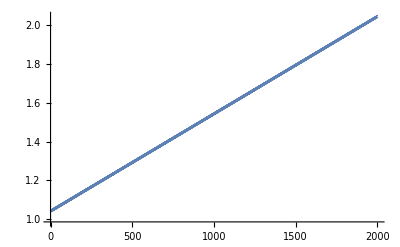

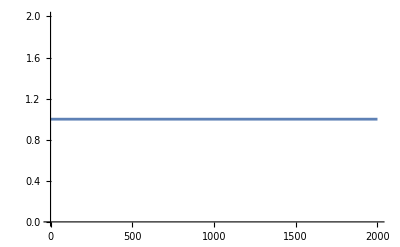

```mathematica
tg=Import["D:\\Curve Elasticity\\Simulation\\2026\\jan\\results\\helicoidC\\st ver - Copy\\taug_2_26_09_22.txt","Table"];
phi=Import["D:\\Curve Elasticity\\Simulation\\2026\\jan\\results\\helicoidC\\st ver - Copy\\phi_2_26_09_22.txt","Table"];
ListLinePlot[Transpose[phi]]
ListLinePlot[Transpose[tg]]
```

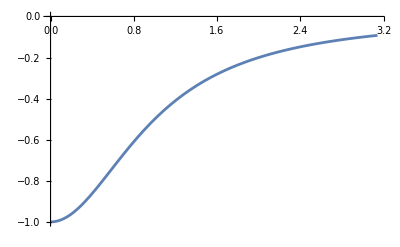

```mathematica
Plot[-1/(1+x^2),{x,0,Pi}]
```